```mathematica
graph=Import[FileNameJoin[{NotebookDirectory[],"data1.dat"}]];

{n,e,r} = graph[[1]];
coords = graph[[2;;n+1]];
edges = graph[[n+2;;]];

lines = Table[Line[{coords[[i]][[1]],coords[[i]][[2]]}],{i,edges}];

index = 1;
vertexNumbers = Table[Text[Style[index++,Blue,Bold,15],i,Right],{i,coords}];

gNodes = Graphics[{PointSize[Large], Red,Point[coords]}];
gGraph=Graphics[{lines,PointSize[Large], Red,Point[coords]}]
(* Blue vertexNumbers*)
```

```mathematica
R=10/Sqrt[13];
X = 100;
Y = 100;
coords2={};
For[i=-X,i≤2*X,i+=3R,
For[j=-Y,j≤2*Y,j+=Sqrt[3]*R,
AppendTo[coords2,{i,j}];
]
]
For[i=-X +3/2R,i≤2*X,i+=3R,
For[j=-Y+Sqrt[3]/2*R,j≤2*Y,j+=Sqrt[3]*R,
AppendTo[coords2,{i,j}];
]
]

coords2=Sort[coords2,(#1[[2]]<#2[[2]])||(#1[[2]]==#2[[2]] && #[[1]]<#2[[1]])&];

tiles=Table[RegularPolygon[p,{R,0},6],{p,coords2}];

index = 1;
zoneNumbers = Table[Text[index++,i],{i,coords2}];

gTiles = Graphics[{EdgeForm[Black],FaceForm[White],tiles, zoneNumbers}];
```

```mathematica
res = Show[{gTiles,gGraph}]
```

```mathematica
tiles = {RegularPolygon[{-6,-6},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(5 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(5 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(5 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(5 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6,-6+5 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+5 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+5 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+5 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+5 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(15 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(15 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(15 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(15 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6,-6+10 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+10 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+10 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+10 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+10 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(25 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(25 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(25 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(25 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6,-6+15 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+15 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+15 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+15 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+15 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(35 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(35 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(35 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(35 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6,-6+20 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+20 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+20 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+20 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+20 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(45 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(45 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(45 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(45 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6,-6+25 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+25 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+25 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+25 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+25 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(55 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(55 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(55 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(55 √(3/13))/2},{5/(√13),0},6],RegularPolygon[{-6,-6+30 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+30 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+30 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+30 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+30 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(2 √13),-6+(5 √39)/2},{5/(√13),0},6],RegularPolygon[{-6+45/(2 √13),-6+(5 √39)/2},{5/(√13),0},6],RegularPolygon[{-6+75/(2 √13),-6+(5 √39)/2},{5/(√13),0},6],RegularPolygon[{-6+105/(2 √13),-6+(5 √39)/2},{5/(√13),0},6],RegularPolygon[{-6,-6+35 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+15/(√13),-6+35 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+30/(√13),-6+35 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+45/(√13),-6+35 √(3/13)},{5/(√13),0},6],RegularPolygon[{-6+60/(√13),-6+35 √(3/13)},{5/(√13),0},6]}
```

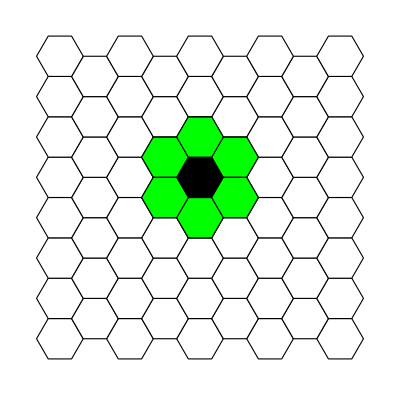

```mathematica
Graphics[{EdgeForm[Black],FaceForm[White],tiles, Black,tiles[[39]],Green,tiles[[{30,34,35,43,44,48}]]}]
```

```mathematica
Export["rr2.png",res]
```

rr2.png